```mathematica
LogisticSegments[r_,x0_,its_]:=Module[
{l=NestList[r*#-(1+r)*#^3&,x0,its]},
Partition[Flatten[Transpose[{l,l}]],2,1]
]
u=1.5
p2=Partition[LogisticSegments[u,0.1,7],2,1];
movie=Table[Plot[{u x-(1+u)x^3,x},{x,0,1},PlotStyle->{{},Dashing[{.02}]},
Prolog->MapIndexed[{Hue[#2[[1]]/Length[p2]],Line[#]}&,Take[p2,i]],
AspectRatio->Automatic,
AxesLabel->TraditionalForm/@{Subscript[x, n],Subscript[x, n+1]}
],{i,Length[p2]}];
movie=Table[Plot[{u x-(1+u)x^3,x},{x,-1,1},PlotStyle->{{},Dashing[{.02}]},
Prolog->MapIndexed[{Hue[#2[[1]]/Length[p2]],Line[#]}&,Take[p2,i]],
AspectRatio->Automatic,
AxesLabel->TraditionalForm/@{Subscript[Z, t],Subscript[x, t+1]}
],{i,Length[p2]}];
ListAnimate[movie]
```

```mathematica
Last[movie]
```

```mathematica
Export["D:\\school_work\\thesis\\presentation\\figures\\INSERT NAME.pdf",Last[movie]]
```

```mathematica
Export["D:\\school_work\\thesis\\presentation\\figures\\INSERT NAME.swf",ListAnimate[movie]]
```

General::munfl: (-7.70763×10^-105)^3 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-4.72368×10^-109)^3 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.89494×10^-113)^3 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

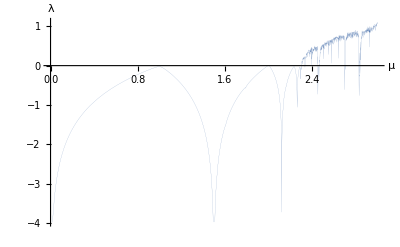

```mathematica
λ[r_]:=Module[{f,l},f[x_]:=r x -(1+r)x^3;
l[x_]:=Log[Abs[r-3(r+1)x^2]];
Mean[l[NestList[f,0.1,1*^2]]]];
Plot[λ[r],{r,0,3},PlotStyle->Thickness[.0001],AxesLabel->{"μ","λ"}]
```

```mathematica
Export["D:\\school_work\\thesis\\presentation\\figures\\lyapunov.pdf",%32]
```

D:\school_work\thesis\presentation\figures\lyapunov.pdf